# Data generation

## TODO

datan.answer.tsv の出力

## Data format

### general information

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

### answer form

< x1 >[\tab]< y2 >[\tab]...[\tab]<cl1>
< x2 >[\tab]< y2 >[\tab]...[\tab]<cl2>
...

## Preparation

```mathematica
(*dir="/Users/amanokou/gitsrc/"*)
```

```mathematica
dir="/home/kamano/gitsrc/"
```

/home/kamano/gitsrc/

```mathematica
(*dir="/Users/kouamano/gitsrc/"*)
```

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation/generative-data"]
```

/home/kamano/gitsrc/ClusteringAdequation/generative-data

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
id=1
```

1

```mathematica
anntS[id]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[id]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[id] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[id]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.73205

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/2.5}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

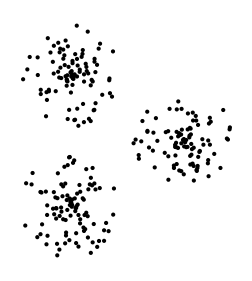

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.00122729,-0.0160274}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

1.04389

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.999757,-0.0223476},{-0.488364,0.87269},{-0.507711,-0.898425}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.320523,0.325768,0.358947}

Export 4f iles:

```mathematica
Export["data1.tsv",strDataToExportStr[id],"String"]
```

data1.tsv

```mathematica
Export["data1.ans.tsv",samplesWithCl[id]]
```

data1.ans.tsv

```mathematica
Export["data1.ans.totalR",totalR[id],"Table"]
```

data1.ans.totalR

```mathematica
Export["data1.ans.clRs",clRs[id],"Table"]
```

data1.ans.clRs

### data 2 (unbalanced)

```mathematica
id=2
```

2

```mathematica
anntS[id]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={200,100,50};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[id]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[id]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.01673

```mathematica
radius[id]={distMean[id]*0.5,distMean[id]*0.35,distMean[id]*0.17}
```

{0.508366,0.355856,0.172845}

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,radius[id][[n]]}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

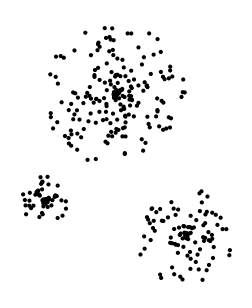

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0773355,-0.392963}

全サンプルの平均半径

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

0.577347

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.00685672,-0.00270844},{0.510366,-0.999878},{-0.50681,-0.740152}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.258715,0.178183,0.0888043}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data2.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data2.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data2.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data2.ans.clRs

### data 4 (sub class)

```mathematica
id=4
```

4

```mathematica
anntS[id]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[id]=2;
numClass[id]=4;
numSample[id]={100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[id]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

3.49071

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/5}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{2.6563,-2.65812},{1.62987,-1.67729}}

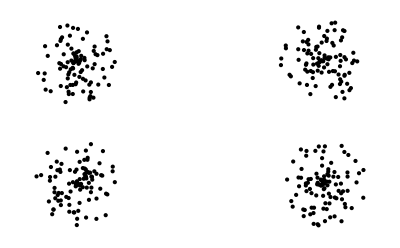

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.00745122,-0.0148398}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.25421

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{2.0039,1.02253},{2.01306,-1.02991},{-1.99414,0.938968},{-1.99302,-0.990947}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.353565,0.358155,0.33789,0.344388}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data4.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data4.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data4.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data4.ans.clRs

### data 5 (ring + disc)

```mathematica
id=5
```

5

```mathematica
anntS[id]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[id]=2;
numClass[id]=2;
numSample[id]={100,200};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[id]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
samples[id,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[id][[1]]}]];
```

```mathematica
samples[id,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[id][[2]]}]];
```

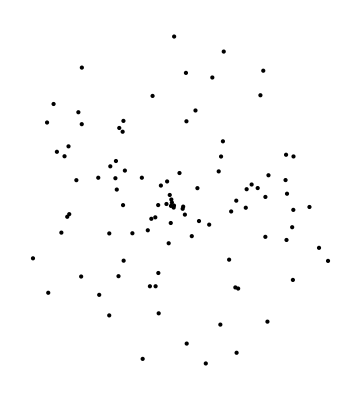

```mathematica
Graphics[Map[Point[#]&,samples[id,"disc"]]]
```

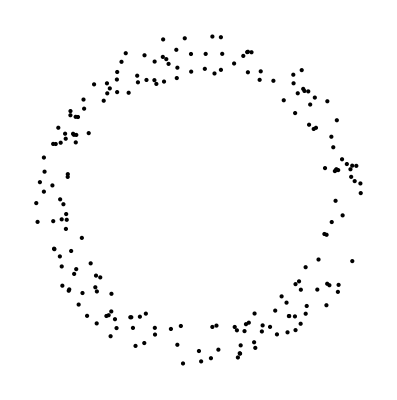

```mathematica
Graphics[Map[Point[#]&,samples[id,"ring"]]]
```

```mathematica
samples[id,"class"]=List[samples[id,"disc"],samples[id,"ring"]];
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

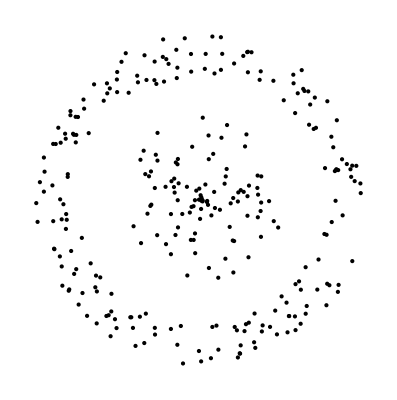

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0443192,0.00104932}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.34506

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0354289,0.0154739},{-0.0841932,-0.00616297}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.519632,1.75442}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data5.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data5.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data5.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data5.ans.clRs

### data 6 (spiral)

```mathematica
id=6
```

6

```mathematica
anntS[id]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[id]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[id,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,0]=Mean[samples[id,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[id,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,1]=Mean[samples[id,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[id,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,2]=Mean[samples[id,2]]
```

{0.25958,-0.22895}

```mathematica
centers[id]={center[id,0],center[id,1],center[id,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[id,"class"]=List[samples[id,0],samples[id,1],samples[id,2]];
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

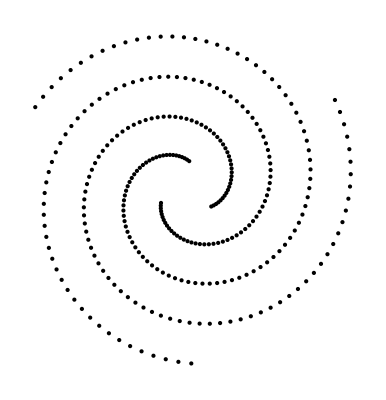

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-1.12503×10^-16,4.81097×10^-17}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.7375

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.71971,1.71971,1.71971}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data6.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data6.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data6.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data6.ans.clRs

## 3D

### data 7 (chain)

```mathematica
id=7
```

7

```mathematica
anntS[id]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[id]=3;
numClass[id]=2;
numSample[id]={150,150};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[id]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0	0
1	0	0

```mathematica
samples[id,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[id,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[id,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[id,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[id,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[id,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(samples[id,"class"]=List[samples[id,1],Map[#+centers[id][[2]]&,samples[id,2]]]//N)//Length
```

2

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.5,-2.7293×10^-18,2.96059×10^-18}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.06354

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{5.92119×10^-18,-5.4586×10^-18,0.},{1.,0.,5.92119×10^-18}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.,1.}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data7.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data7.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data7.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data7.ans.clRs

## Many class

### data 8 (4 classes)

```mathematica
id=8
```

8

```mathematica
anntS[id]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[id]=2;
numClass[id]=4;
numSample[id]={100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[id]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

4.55228

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/4}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{3.07992,-3.05975},{3.05733,-3.09508}}

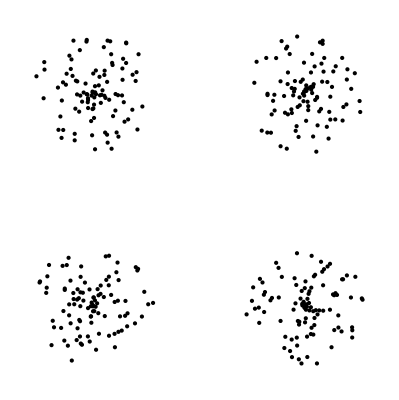

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.0210565,0.00443314}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.8733

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{2.02338,1.99818},{2.02881,-2.01945},{-1.9486,2.01756},{-2.01937,-1.97856}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.568874,0.592192,0.584152,0.573782}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data8.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data8.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data8.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data8.ans.clRs

### data 9 (8 classes)

```mathematica
id=9
```

9

```mathematica
anntS[id]="Model: central random , circles, one radius, 2d-8class.\n"
```

Model: central random , circles, one radius, 2d-8class.

```mathematica
dim[id]=2;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]={{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}
```

{{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

7	7
7	-7
-7	7
-7	-7
0	20
20	0
0	-20
-20	0

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

22.4998

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/4.2}],RandomReal[{0,2Pi}]}],{numSample[9][[n]]}]],{n,numClass[9]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{25.1417,-24.7598},{24.8311,-24.5281}}

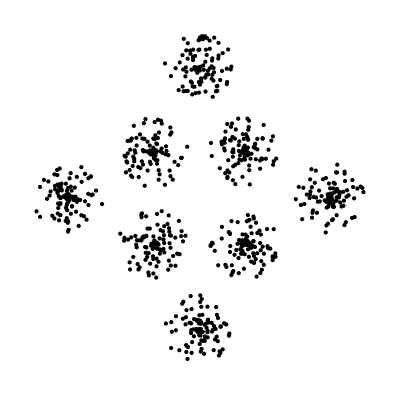

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[9,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.0776602,0.061864}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

15.2262

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{6.7648,7.38536},{7.29734,-7.34967},{-7.37944,7.02562},{-6.79007,-7.00631},{0.399808,20.0345},{20.084,0.212171},{0.275979,-19.9649},{-20.0312,0.15812}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{2.62478,2.68842,2.67454,2.6753,2.8466,2.54703,2.48888,2.4659}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data9.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data9.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data9.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data9.ans.clRs

### data 10 (3d-8 classes) (scale: base)

```mathematica
id=10
```

10

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class (base).\n"
```

Model: central random , circles, one radius, 3d-8class (base).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0	0
0	0	10
0	10	0
0	10	10
10	0	0
10	0	10
10	10	0
10	10	10

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

12.821

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/16]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{12.3604,-2.62676},{12.5977,-2.16931},{12.1806,-2.07261}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{5.00966,5.00192,5.02942}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

8.7263

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.0466647,0.0239928,0.076734},{0.112273,-0.0463527,9.97213},{0.0223635,10.0051,-0.00683801},{-0.0182618,10.0202,9.91654},{9.96467,0.0769035,0.160905},{10.1326,-0.0985181,9.97516},{9.96569,9.9271,-0.0170012},{9.94456,10.1069,10.1577}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.36804,1.38691,1.31291,1.22136,1.28719,1.25502,1.34258,1.25917}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data10.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data10.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data10.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data10.ans.clRs

### data 10.2 (3d-8 classes) (scale: 2)

```mathematica
id=10.2
```

10.2

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled.\n"
```

Model: central random , circles, one radius, 3d-8class, scaled.

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/4//N
```

{{0.,0.,0.},{0.,0.,2.5},{0.,2.5,0.},{0.,2.5,2.5},{2.5,0.,0.},{2.5,0.,2.5},{2.5,2.5,0.},{2.5,2.5,2.5}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n";
```

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

3.20525

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/10]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{3.38775,-0.974062},{3.48036,-1.15067},{3.66917,-0.966026}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{1.25083,1.24505,1.24455}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.24135

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.0225536,0.0453529,-0.0419678},{0.00233656,-0.0714724,2.52124},{0.00298844,2.51806,-0.0834598},{-0.0173286,2.50201,2.50522},{2.55303,-0.0235075,-0.0535753},{2.50589,-0.0385014,2.50915},{2.47686,2.45945,0.0746803},{2.50544,2.56899,2.52508}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.517943,0.545823,0.470798,0.556161,0.517299,0.524165,0.514887,0.514415}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-2.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-2.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-2.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-2.ans.clRs

### data 10.3 (3d-8 classes) (scale: 3)

```mathematica
id=10.3
```

10.3

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(3).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(3).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/10]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.74892,-0.556394},{1.68777,-0.462671},{1.77235,-0.451744}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.622543,0.625225,0.623412}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.10214

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.00687179,0.00433035,0.00917509},{-0.00341285,0.00181045,1.24058},{0.0118571,1.26522,0.00818636},{-0.00198643,1.25587,1.25295},{1.23854,0.00927695,-0.00155592},{1.23018,-0.0101165,1.22553},{1.2536,1.23843,-0.011654},{1.24468,1.23698,1.26408}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.263691,0.267438,0.272764,0.253117,0.246885,0.263202,0.262504,0.259898}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-3.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-3.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-3.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-3.ans.clRs

### data 10.4 (3d-8 classes) (scale: 4)

```mathematica
id=10.4
```

10.4

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(4).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(4).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/15]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.57574,-0.391217},{1.60577,-0.334626},{1.65544,-0.277694}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.620684,0.627577,0.621612}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09029

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.00422868,0.000711437,-0.00358775},{-0.00538128,0.00702086,1.23757},{-0.00255109,1.24637,0.00303473},{-0.00424147,1.26303,1.24236},{1.25205,-0.0136161,0.000535801},{1.25437,0.004575,1.24918},{1.24427,1.24583,0.0100902},{1.22272,1.26669,1.23371}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.176164,0.178925,0.168292,0.182626,0.178689,0.164204,0.165569,0.161616}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-4.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-4.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-4.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-4.ans.clRs

## Noisy

### data 3 (noisy)(old)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.56435,-1.0105},{1.36032,-1.43595}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

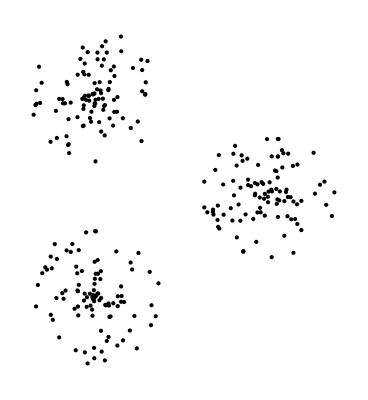

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

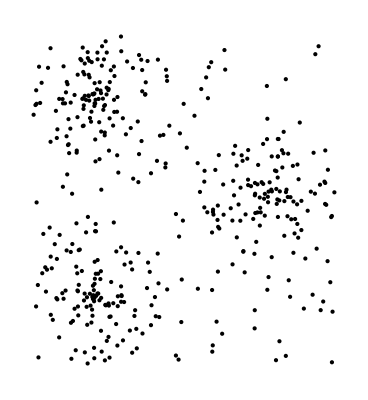

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*(samples[3,"All"]=Append[samples[3,"class"],samples[3,"background"]])//Length*)
```

全サンプルの平均半径

```mathematica
id=3
```

3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0122606,0.00326999}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.01003

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.958673,0.0158914},{-0.500193,0.852192},{-0.495261,-0.858274}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.306362,0.275759,0.287733}

```mathematica
Export["data3.tsv",strDataToExportStr[3],"String"]
```

data3.tsv

```mathematica
Export["data3.ans.totalR",totalR[id],"Table"]
```

data3.ans.totalR

```mathematica
Export["data3.ans.clRs",clRs[id],"Table"]
```

data3.ans.clRs

## high Dimensional

## Experimental